### speed-density

```mathematica
SetDirectory[NotebookDirectory[]];
l = 5; (* m - length of a car *)
ρ0=1/105.; (* cars/m - empty density *)
τf = 2; (* s - safe following time *)
ve[ρ_]:=(1/(ρ+ρ0)-l)/τf;
```

```mathematica
ρj=1/l-ρ0
vl=ve[0]
```

0.190476

50.

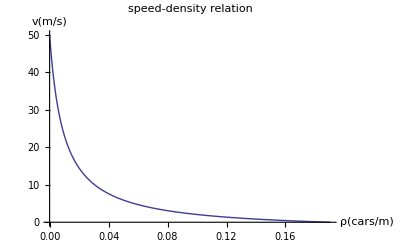

speed-density.png

```mathematica
Plot[ve[ρ],{ρ,0,ρj},PlotRange->All,PlotLabel->"speed-density relation",AxesLabel->{"ρ(cars/m)","v(m/s)"}]
Export["speed-density.png",%]
```

### flow

```mathematica
Q[ρ1_,ρ2_]:=ve[ρ1]*ρ1+ve[ρ2]*ρ2
Plot3D[Q[ρ1,ρ2],{ρ1,0,ρj},{ρ2,0,ρj},PlotLabel->"traffic flow of an unregulated two-lane freeway",AxesLabel->{"ρ1(cars/m)","ρ2(cars/m)","Q(cars/s)"}]
Export["unregulated_flow.png",%]
```

-Graphics3D-

unregulated_flow.png

### rule

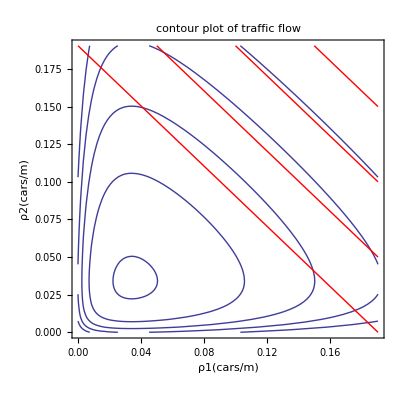

../paper/plot/contour_flow.png

```mathematica
rule=Plot[ρ1,{ρ1,0,ρj},Frame->{True,True,True,True}];
Show[
Join[
Table[
ContourPlot[Q[ρ1,ρ2]==q,{ρ1,0,ρj},{ρ2,0,ρj},PlotLabel->"contour plot of traffic flow",FrameLabel->{"ρ1(cars/m)","ρ2(cars/m)"}]
,{q,.2,.6,.1}]
,Table[
ContourPlot[ρ1+ρ2==p,{ρ1,0,ρj},{ρ2,0,ρj},ContourStyle->Red]
,{p,ρj,2ρj,0.05}]
]

]
Export["../paper/plot/contour_flow.png",%]
```